```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
If[($OperatingSystem=="Windows"),<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m",
<< "/Users/oliviercroissant/Documents/Math/BS.m"]
```

```mathematica
<<"PlotLegends`"
```

```mathematica
Off[FindRoot::"precw"]
```

```mathematica
ss=Simplify[Integrate[1/((ϵ+F^2)^(β/2)),{F,F0,K}],Im[K]==0&&Im[F0]==0&&F0-K≠0&&ϵ>0]
```

1/((-2+β) ϵ)(1/F0(F0^2+ϵ)^(1-β/2) ((F0^2+ϵ) Hypergeometric2F1[1,3/2-β/2,-1/2,-F0^2/ϵ]+(F0^2 (-5+β)-ϵ) Hypergeometric2F1[1,3/2-β/2,1/2,-F0^2/ϵ])-1/K(K^2+ϵ)^(1-β/2) ((K^2+ϵ) Hypergeometric2F1[1,3/2-β/2,-1/2,-K^2/ϵ]+(K^2 (-5+β)-ϵ) Hypergeometric2F1[1,3/2-β/2,1/2,-K^2/ϵ]))

```mathematica
Integrate[1/((ϵ+F^2)^(β/2)),F]
```

F (1+F^2/ϵ)^(β/2) (F^2+ϵ)^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ]

```mathematica
zz[K_,F0_,ϵ_,β_]:=K ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-K^2/ϵ]-F0 ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F0^2/ϵ]
```

```mathematica
ss0=Simplify[Integrate[1/(F^β),{F,F0,K}],Im[K]==0&&Im[F0]==0&&F0-K≠0&&ϵ>0]
```

If[(F0/(F0-K)≤0&&F0≠0)||K/(F0-K)≥0,F0^(1-β)/(-1+β)-K^(1-β)/(-1+β),Integrate[F^-β,{F,F0,K},Assumptions→!(((Im[F0]≥Im[K]&&Im[K] Re[F0]≤Im[F0] Re[K])||(Im[K] Re[F0]≥Im[F0] Re[K]&&Im[F0]≤Im[K]))&&((Re[F0/(-F0+K)]≥0&&F0/(F0-K)≠0)||F0/(-F0+K)∉Reals||Re[F0/(F0-K)]≥1))]]

```mathematica
zz0[K_,F0_,β_]:=F0^(1-β)/(-1+β)-K^(1-β)/(-1+β)
```

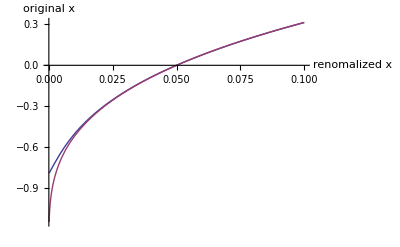

```mathematica
Module[{F0=0.05,β=0.7,ϵ=0.00004},
Plot[{zz[K,F0,ϵ,β],zz0[K,F0,β]},{K,0.0001,0.1},PlotLegend->{"F_ϵ","F_0"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

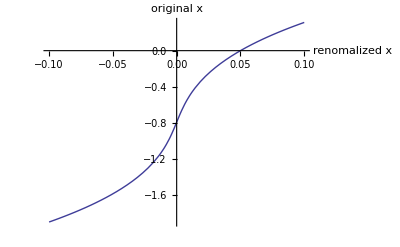

```mathematica
Module[{F0=0.05,β=0.7,ϵ=0.00004},
Plot[{zz[K,F0,ϵ,β]},{K,-0.1,0.1},PlotLegend->{"F_ϵ","F_0"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

```mathematica
LocalVolCall[CC_,CCDev1_,CCDev2_,CCInvInteg_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav},
fav=(F+K)/2;
w=1/(√(2 T))(CCInvInteg[K]-CCInvInteg[F]);
H1=2(ⅇ^(-w^2)+√(π w^2)(NormDis[√2 Abs[w]]-1));
H2=2/3(ⅇ^(-w^2)(1-2 w^2)-2(Abs[w])^3 √π(NormDis[√2 Abs[w]]-1));
Q=CC[fav]^2/4((CCDev2[fav]/CC[fav])-1/2(CCDev1[fav]/CC[fav])^2);
Max[F-K,0]+(√(CC[K] CC[F] T))/(2 √(2π))(H1+T H2 Q)
]
```

```mathematica
Simplify[D[alpha (F^2+epsilon)^(beta/2),F,F]]
```

alpha beta (epsilon+F^2)^(-2+beta/2) (epsilon+(-1+beta) F^2)

```mathematica
SABRCC[F_,alpha_,beta_,epsilon_]:=alpha (F^2+epsilon)^(beta/2)
```

```mathematica
SABRCCDev1[F_,alpha_,beta_,epsilon_]:=alpha beta F (epsilon+F^2)^(-1+beta/2)
```

```mathematica
SABRCCDev2[F_,alpha_,beta_,epsilon_]:=alpha beta (epsilon+F^2)^(-2+beta/2) (epsilon+(-1+beta) F^2)
```

```mathematica
SABRCCInvInteg[F_,alpha_,β_,ϵ_]:=alpha F (1+F^2/ϵ)^(β/2) (F^2+ϵ)^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ]
```

```mathematica
SABRCall[F_,K_,vol_,T_,beta_,epsilon_]:=
Module[{},
LocalVolCall[(SABRCC[#,vol,beta,epsilon])&,(SABRCCDev1[#,vol,beta,epsilon])&,(SABRCCDev2[#,vol,beta,epsilon])&,(SABRCCInvInteg[#,vol,beta,epsilon])&,F,K,T]
]
```

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5,ϵ=0.000001,K=0.06},
    {SABRCall[F, K, vol, T, beta,ϵ]}]
```

{0.0121818}

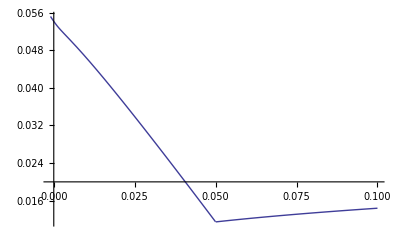

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5,ϵ=0.00001},
    Plot[{SABRCall[F, K, vol, T, beta,ϵ]},{K,-0.001,0.1}]]
```

# Debut de l' etude

```mathematica
Le processus est :
```

```mathematica
{{{Subscript[dF, ϵ,t]=Subscript[α, t](ϵ+Subscript[F, ϵ,t]^2)^(β/2)Subscript[dW, t]}, {Subscript[dα, t]=ν Subscript[α, t] Subscript[dW', t]}}
```

```mathematica
avec
```

```mathematica
Subscript[dW, t].OverTilde[Subscript[dW, t]]=ρ dt
```

```mathematica
{{{D[P, t]=1/2  α^2 C[F]^2(∂^2 P)/(∂F^2)+1/2  ν^2 α^2(∂^2 P)/(∂α^2)+ ν ρ α^2 C[F](∂^2 P)/(∂α∂F)}, {P[0]=(1/2 α^2 C[K]^2)δ[f-K]}}
```

```mathematica
V[T,F,α]=SuperPlus[(F-K)]+∫_0^T ⅆtP[t,F,α]
```

```mathematica
{{{-D[V, t]=1/2  α^2 C[F]^2(∂^2 V)/(∂F^2)+1/2  ν^2 α^2(∂^2 V)/(∂α^2)+ ν ρ α^2 C[F](∂^2 V)/(∂α∂F)}, {V[T,F,α]=Max{F-K,0}}}
```

```mathematica
{{{D[P, t]=1/2  (1-2 ρ ν z+ν^2 z^2)(∂^2 P)/(∂z^2)+1/2  ν^2 α^2(∂^2 P)/(∂α^2)-1/2 α B'/B(∂P)/(∂z)+ ( ρ ν-ν^2 z)(α(∂^2 P)/(∂α∂z)-(∂P)/(∂z))}, {P[0]= α/C[K] δ[z]}}
```

```mathematica
ϕ[({{F}, {α/ν}})]=({{1/(√(1-ρ^2))(∫_p^F 1/C[u] ⅆu-ρ α/ν)}, {α/ν}})
```

```mathematica
x=1/ν∫_0^(ν z) 1/(√(1-2ρ ζ+ζ^2))ⅆζ
```

```mathematica
∫_p^F 1/C[u] ⅆu
```

```mathematica
∫_0^F 1/((ϵ+u^2)^(β/2))ⅆu=F ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ]
```

```mathematica
∫_p^F 1/((u^2)^(β/2))ⅆu
```

If[Re[β]<1,(F Abs[F]^-β)/(1-β),Integrate[F Abs[F u]^-β,{u,0,1},Assumptions→Re[β]≥1]]

```mathematica
∫_p^F 1/((u^2)^(β/2))ⅆu=(F Abs[F]^-β)/(1-β)-(p Abs[p]^-β)/(1-β)
```

```mathematica
V[T,F,α]=[F-K]^++1/2 α √(C[K]C[F])(1-2ρ ν z+ν^2 z^2)^(1/4)ⅇ^(1/4 ρ ν α C'[(F+K)/2] z^2)Φ[T,M]
```

```mathematica
Φ[T,M]=∫_0^T Q[t,M]ⅆt
```

```mathematica
Soit
 M=ν^2(1/4 Subscript[I, 2] I-1/8(Subscript[I, 1])^2)+α^2(1/4 Subscript[b, 2]-3/8 Subscript[b, 1]^2)+3/4 ρ ν α Subscript[b, 1];
Subscript[b, 1]=C'[(F+K)/2];
```

```mathematica
α dz=dF/C(F)
```

```mathematica
soit C(F)=dF/(α dz)
```

```mathematica
B(α z)=C(F)
```

```mathematica
donc B'(α z) α dz=C'(F) dF
```

```mathematica
donc B'=C' C
```

```mathematica
B''(α z) α dz=C'' dF C+(C')^2 dF
```

```mathematica
donc B''=(C'' C+(C')^2)C
```

```mathematica
Subscript[b, 2]=B''/B==C''[(F+K)/2]C[(F+K)/2]+Subscript[b, 1]^2
```

```mathematica
I=√(1+z ν (z ν-2 ρ));
Subscript[I, 1]=(z ν-ρ)/I;
Subscript[I, 2]=(1-ρ^2)/I^3;
```

```mathematica
Subscript[Q, τ]=1/2 Subscript[Q, xx]+M Q
```

```mathematica
Q[x_,t_]:=1/(√(2π t))ⅇ^(-x^2/(2t)+M t)
```

```mathematica
Calcul de la charge :
```

```mathematica
1/4 Subscript[I, 2] I-1/8(Subscript[I, 1])^2=(1-ρ^2)/(4 I^2)-1/8(z ν-ρ)^2/I^2=1/8((2-2 ρ^2-(z ν-ρ)^2)/(1+z ν (z ν-2 ρ)))=1/8((2-2 ρ^2-z^2 ν^2-ρ^2+2z ν ρ)/(1+z ν (z ν-2 ρ)))=1/8((2-3 ρ^2-z ν(z ν-2 ρ))/(1+z ν (z ν-2 ρ)))
```

```mathematica
(1/4 Subscript[b, 2]-3/8 Subscript[b, 1]^2)=(1/4(C''[(F+K)/2]+Subscript[b, 1]^2)-3/8 Subscript[b, 1]^2)=(1/4 C''[(F+K)/2]C[(F+K)/2]-1/8 Subscript[b, 1]^2)=1/8(2C''[(F+K)/2]C[(F+K)/2]-C'[(F+K)/2]^2)
```

```mathematica
dans le cas ou C=(ϵ+F^2)^(β/2)
```

```mathematica
C'=(β/2 )2F (ϵ+F^2)^(β/2-1)=β F (ϵ+F^2)^(β/2-1)
```

```mathematica
C''=β  (ϵ+F^2)^(β/2-1)+β (β/2-1)F 2F(ϵ+F^2)^(β/2-2)=(ϵ+F^2)^(β/2-2)(β( ϵ+F^2) +β (β-2)F^2)=β(ϵ+F^2)^(β/2-2)(ϵ+(β-1)F^2)
```

```mathematica
donc
```

```mathematica
(1/4 Subscript[b, 2]-3/8 Subscript[b, 1]^2)=1/8(ϵ+Subscript[F, avg]^2)^(β/2-2)(2β(ϵ+(β-1)Subscript[F, avg]^2)(ϵ+Subscript[F, avg]^2)^(β/2)-β^2 Subscript[F, avg]^2(ϵ+Subscript[F, avg]^2)^(β/2) )=1/8(ϵ+Subscript[F, avg]^2)^(β-2)(2β(ϵ+(β-1)Subscript[F, avg]^2)-β^2 Subscript[F, avg]^2 )
=1/8(ϵ+Subscript[F, avg]^2)^(β-2)(2β(ϵ+(β-1)Subscript[F, avg]^2)-β^2 Subscript[F, avg]^2 )=1/8(ϵ+Subscript[F, avg]^2)^(β-2)β(2 ϵ+(β-2)Subscript[F, avg]^2)
```

```mathematica
quand ϵ->0 on a : (1/4 Subscript[b, 2]-3/8 Subscript[b, 1]^2)=(-(2-β))/8(Subscript[F, avg])^(2β-2)
```

```mathematica
au total
```

```mathematica
M=ν^2/8((2-3 ρ^2-z ν(z ν-2 ρ))/(1+z ν (z ν-2 ρ)))+α^2/8(ϵ+Subscript[F, avg]^2)^(β-2)β(2 ϵ+(β-2)Subscript[F, avg]^2)+3/4 ρ ν α β Subscript[F, avg](ϵ+Subscript[F, avg]^2)^(β/2-1);
```

```mathematica
dans l'hypothese ν et  α petit on a :
```

```mathematica
M=ν^2/8(2-3 ρ^2)+α^2/8(ϵ+Subscript[F, avg]^2)^(β-2)β(2 ϵ+(β-2)Subscript[F, avg]^2)+3/4 ρ ν α β Subscript[F, avg](ϵ+Subscript[F, avg]^2)^(β/2-1);
```

```mathematica
et
```

```mathematica
quand ϵ->0 on a :
```

```mathematica
M=ν^2/8(2-3 ρ^2)+α^2/8(Subscript[F, avg])^(2β-4)(β(β-2)Subscript[F, avg]^2)+3/4 ρ ν α β Subscript[F, avg](Subscript[F, avg])^(β-2)=ν^2/8(2-3 ρ^2)-α^2/8 β(β-2)(Subscript[F, avg])^(2β-2)+3/4 ρ ν α β (Subscript[F, avg])^(β-1)
```

```mathematica
dans le cas ou on suppose (Subscript[F, avg])=K , on a bien :
```

```mathematica
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
```

```mathematica
∫_T0^T 1/(√(2π t))ⅇ^(-x^2/(2t)+M t)ⅆt
```

1/(√(2 π))If[((Im[T]≥Im[T0]&&Im[T0] Re[T]≤Im[T] Re[T0])||(Im[T0] Re[T]≥Im[T] Re[T0]&&Im[T]≤Im[T0]))&&((Re[T0/(T-T0)]≥0&&T0/(T-T0)≠0)||T0/(T-T0)∉Reals||1+Re[T0/(T-T0)]≤0),1/(2 √-M)ⅇ^(-√2 √-M √(x^2)) √π (Erf[√-M √T-(√(x^2))/(√2 √T)]+ⅇ^(2 √2 √-M √(x^2)) Erf[√-M √T+(√(x^2))/(√2 √T)]-Erf[√-M √T0-(√(x^2))/(√2 √T0)]-ⅇ^(2 √2 √-M √(x^2)) Erf[√-M √T0+(√(x^2))/(√2 √T0)]),Integrate[(ⅇ^(M t-x^2/(2 t)))/(√t),{t,T0,T},Assumptions→!(((Im[T]≥Im[T0]&&Im[T0] Re[T]≤Im[T] Re[T0])||(Im[T0] Re[T]≥Im[T] Re[T0]&&Im[T]≤Im[T0]))&&((Re[T0/(T-T0)]≥0&&T0/(T-T0)≠0)||T0/(T-T0)∉Reals||1+Re[T0/(T-T0)]≤0))]]

```mathematica
Erf[100.1]
```

1.

```mathematica
Simplify[1/(2 √-M)ⅇ^(-√2 √-M x) √π (Erf[√-M √T-x/(√2 √T)]+ⅇ^(2 √2 √-M x) Erf[√-M √T+x/(√2 √T)]+1-ⅇ^(2 √2 √-M x) )]
```

(ⅇ^(-√2 √-M x) √π (1-ⅇ^(2 √2 √-M x)+Erf[√-M √T-x/(√2 √T)]+ⅇ^(2 √2 √-M x) Erf[√-M √T+x/(√2 √T)]))/(2 √-M)

```mathematica
∫_0^T 1/(√(2π t))ⅇ^(-x^2/(2t)+M t)ⅆt=(ⅇ^(-√2 √-M x) √π (1-ⅇ^(2 √2 √-M x)+Erf[√-M √T-x/(√2 √T)]+ⅇ^(2 √2 √-M x) Erf[√-M √T+x/(√2 √T)]))/(2 √-M)
```

```mathematica
ΦSAbr[T_,x_,M_]:=Re[1/(2 √-M)ⅇ^(-√2 √-M x) √π (1-ⅇ^(2 √2 √-M x)+ⅇ^(2 √2 √-M x) Erf[x/(√2 √T)+√-M √T]-Erf[x/(√2 √T)-√-M √T])]
```

```mathematica
{{{{GIntegralAnalytical4[a_,b_,T_]:=Re[(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)]))/(2 a)]}}}}
```

```mathematica
Module[{T=2,M=0.8,x=0.1},{ΦSAbr[T,x,M],GIntegralAnalytical4[√-M,x,T],√2 GIntegralAnalytical[√-M/√2,x,√(2T)]}]
```

{5.19282,5.19282,1.60054}

```mathematica
Clear[VSAbr]
```

```mathematica
SABROptionAnalyticOption[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=0,
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z]];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
If[z==0,call=(K^β α)/(2 √(2 π)) ΦSAbr[T,Abs[x],κ],
call=N[Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x ΦSAbr[T,Abs[x],κ]]];
call];
```

```mathematica
SABROptionAnalyticVol[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{call},
call=SABROptionAnalyticOption[f,α,β,ρ,ν,K,T];
ImpVolBS[f,K,T,1,call]];
```

```mathematica
SABROptionAnalyticNVol[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{call},
call=SABROptionAnalyticOption[f,α,β,ρ,ν,K,T];
NormalImplicitVol[f,K,T,call]];
```

```mathematica
SABRHaganVol[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat},z=(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Effetmat=(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T)/(1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
If[z==0,K^(-1+β) α Effetmat,
α/(f K)^((1-β)/2) z/x  Effetmat  ]]
```

```mathematica
SABRHaganOption[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{vol},
vol=  SABRHaganVol[f,α,β,ρ,ν,K,T];
BS[f,K,T,vol ]]
```

```mathematica
Module[{f=0.05,α=0.0248,T=20,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[{SABROptionAnalyticVol[f,α,β,ρ,ν,K,T],SABRHaganVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

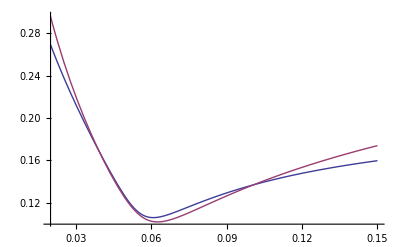

```mathematica
Module[{CVol,IntegInvCVol,β=0.3,ϵ=0.0000001,KList=Table[i 0.001-0.05,{i,1,200}],
T=10,F=0.05,α=0.3,ν=0.5,ρ=-0.4,K=0.0456,preres},
CVol=((#^2+ϵ)^(β/2))&;
IntegInvCVol=(# ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-#^2/ϵ])&;
{VSAbr[CVol,IntegInvCVol,K,T,F,α,ν,ρ],VSAbrVol[CVol,IntegInvCVol,K,T,F,α,ν,ρ],SABROptionAnalyticOption[F,α,β,ρ,ν,K,T],SABRHaganOption[F,α,β,ρ,ν,K,T]}]
```

{{0.0624529,0.0365225,0.036388,-0.502356,2.40736,0.0456},{-0.0344498,0.0365225,0.036383,0.0456},0.0624487,0.05}

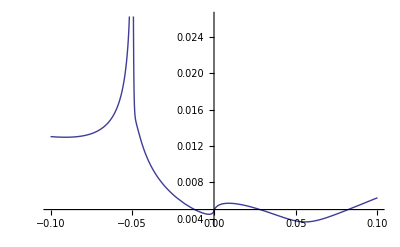

```mathematica
Module[{CVol,IntegInvCVol,β=0.5,ϵ=0.0000001,KList=Table[i 0.001-0.05,{i,1,200}],
T=10,F=0.05,α=0.03,ν=0.5,ρ=-0.4,preres},
CVol=((#^2+ϵ)^(β/2))&;
IntegInvCVol=(# ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-#^2/ϵ])&;
Plot[VSAbrVol[CVol,IntegInvCVol,K,T,F,α,ν,ρ][[1]],{K,-0.1,0.1}]]
```

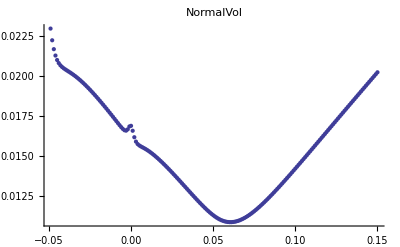
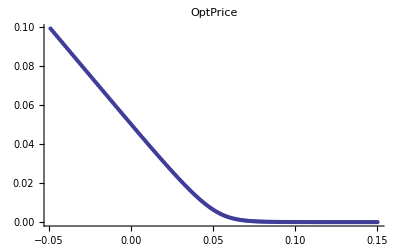
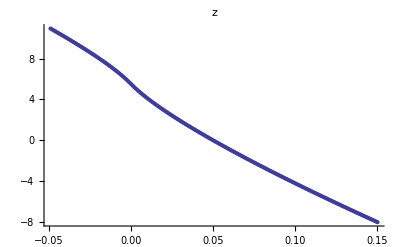
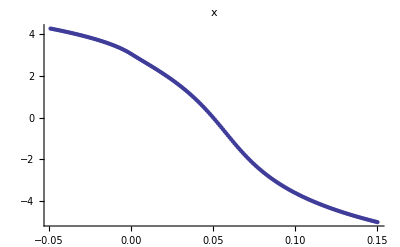
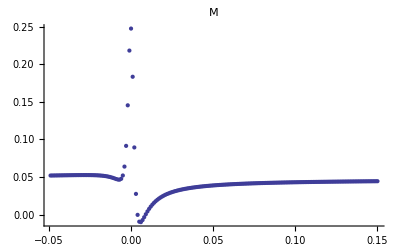
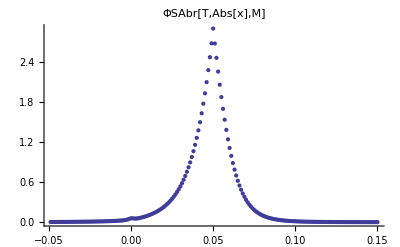

```mathematica
Module[{CVol,IntegInvCVol,β=0.2,ϵ=0.00001,KList=Table[i 0.001-0.05,{i,1,200}],
T=2,F=0.05,α=0.02,ν=0.5,ρ=-0.4,res,preres},
CVol=((#^2+ϵ)^(β/2))&;
IntegInvCVol=(# ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-#^2/ϵ])&;
preres=Map[(VSAbr[CVol,IntegInvCVol,#,T,F,α,ν,ρ])&,KList];
res=Transpose[preres];
(*Print[preres];*)
{ListPlot[Transpose[{KList,MapThread[NormalImplicitVol[F,#1,T,#2]&,{KList,res[[1]]}]}],PlotLabel->"NormalVol"],
ListPlot[Transpose[{KList,res[[1]]}],PlotLabel->"OptPrice"],
ListPlot[Transpose[{KList,res[[2]]}],PlotLabel->"z"],
ListPlot[Transpose[{KList,res[[3]]}],PlotLabel->"x"],
ListPlot[Transpose[{KList,res[[4]]}],PlotLabel->"M"],
ListPlot[Transpose[{KList,res[[5]]}],PlotLabel->"ΦSAbr[T,Abs[x],M]"]}]
```

### CEV Vanilla Closed form

```mathematica
NonCentralChi[ν_,λ_,z_]:=CDF[NoncentralChiSquareDistribution[ν,λ],z]
```

```mathematica
CEVCall[F_,K_,vol_,r_,T_,beta_]:=Module[{Sp,Kp,k=If[r==0,1/(2 vol^2(1-beta)^2 T),r/(vol^2(1-beta)(ⅇ^(r T(2-2beta))-1))]},
Sp=F^(2-2beta)ⅇ^(-r T(2-2beta))k;
Kp=K^(2-2beta)k;
F (1-NonCentralChi[2+2/(2-2beta),2Sp,2Kp])-ⅇ^(-r T)K NonCentralChi[2/(2-2beta),2Kp,2Sp]]
```

```mathematica
CEVCall[F_,K_,vol_,T_,beta_]:=Module[{Sp,Kp,k=1/(2 vol^2(1-beta)^2 T)},
Sp=F^(2-2beta)k;
Kp=K^(2-2beta)k;
F (1-NonCentralChi[2+2/(2-2beta),2Sp,2Kp])-K NonCentralChi[2/(2-2beta),2Kp,2Sp]]
```

```mathematica
CDF[NoncentralChiSquareDistribution[ν,λ],z]
```

∫_0^z 2^(-ν/2) ⅇ^(1/2 (-z2-λ)) z2^(-1+ν/2) Hypergeometric0F1Regularized[ν/2,(z2 λ)/4]ⅆz2

```mathematica
PDF[NoncentralChiSquareDistribution[ν,λ],z]
```

2^(-ν/2) ⅇ^(1/2 (-z-λ)) z^(-1+ν/2) Hypergeometric0F1Regularized[ν/2,(z λ)/4]

```mathematica
CEVCall1[F_,K_,vol_,T_,beta_]:=Module[{Sp,Kp,k=1/(2 vol^2(1-beta)^2 T),Y},
Sp=F^(2-2beta)k;
Kp=K^(2-2beta)k;Y=1/(2-2beta);
F -(∫_0^1 z^Y(ⅇ^(-(Kp z+Sp)) F(Kp )^(1+Y) Hypergeometric0F1Regularized[1+Y,Kp z Sp]+ⅇ^(-(Sp z+Kp)) K (Sp )^Y/z Hypergeometric0F1Regularized[Y,Sp z Kp])ⅆz)]
```

```mathematica
CEVCallDK[F_,K_,vol_,T_,beta_]:=Module[{Sp,Kp,k=1/(2 vol^2(1-beta)^2 T),Y},
Sp=F^(2-2beta)k;
Kp=K^(2-2beta)k;Y=1/(2-2beta);
N[(∫_0^1 z^Y(1/z ⅇ^(-(Kp+ Sp)  (1+z))  (ⅇ^(Sp+Kp z) (2 (-1+beta) k K^(2-2beta)+1) Sp^Y Hypergeometric0F1Regularized[Y,Kp Sp z]-2 (-1+beta) k  z ((ⅇ^(Sp+Kp  z) K^(2-2 beta) Sp^(1+Y)+ⅇ^(Kp+Sp z) F   k^Y (K^(2-2 beta) (1+Y)-k K^(4-4beta) z)) Hypergeometric0F1Regularized[1+Y,Kp  Sp z]+ⅇ^(Kp+Sp z) F k K^(4-4beta) k^Y Sp z Hypergeometric0F1Regularized[2+Y,Kp  Sp z])))ⅆz)]]
```

```mathematica
CEVBSVol[F_,K_,vol_,drift_,T_,beta_]:=ImpVolBS[F,K,T,CEVCall[F,K,vol,drift,T,beta]]
```

```mathematica
Module[{F = 0.05, vol = 0.06, beta = .9995, T = 10, drift = 0, K = 0.07},
CEVBSVol[F,K,vol,drift,T,beta]]
```

0.0600848827658801941364813766303

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5,K=0.06},
  {  N[CEVCall1[F, K, vol, T, beta]],CEVCall[F, K, vol, T, beta]}]]
```

{0.892775,{0.0078957,0.0078957}}

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5,K=0.06},
  {  CEVDistribution[F, K, vol,0, T, beta],N[CEVCallDK[F, K, vol, T, beta]]}]]
```

{1.99558,{0.301175,0.301175}}

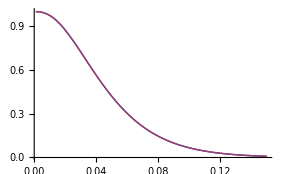

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5},
    Plot[ {  CEVDistribution[F, K, vol,0, T, beta],CEVCallDK[F, K, vol, T, beta]},{K,0.001,0.15},PlotRange->All]]
```

```mathematica
on  Kp ->0 et K^(2-2beta)->0
```

```mathematica
CEVCallDK0[F_,vol_,T_,beta_]:=Module[{Sp,Kp,k=1/(2 vol^2(1-beta)^2 T),Y},
Sp=F^(2-2beta)k;
Y=1/(2-2beta);
∫_0^1 z^(Y-1)ⅇ^(- Sp  z)  Sp^Y Hypergeometric0F1Regularized[Y,0]ⅆz]
```

```mathematica
(Kp)^Y=K^((2-2beta)/(2-2beta))k^(1/(2-2beta))=K  k^Y
```

```mathematica
ce qui se met sous la forme
```

```mathematica
CEVCallDK0[F_,vol_,T_,beta_]:=Module[{Sp,Kp,k=1/(2 vol^2(1-beta)^2 T),Y},
Sp=F^(2-2beta)k;
Y=1/(2-2beta);
(Gamma[Y]-Gamma[Y,Sp])/Gamma[Y]]
```

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.6, T = 20.5,K=0.06},
  N[CEVCallDK0[F, vol, T, beta]]]]
```

{0.,0.347461}

```mathematica
CEVDensity[F_,K_,vol_,T_,beta_]:=Module[{shift=0.0001},-(CEVCallDK[F,K+shift,vol,T,beta]-CEVCallDK[F,K-shift,vol,T,beta])/(2shift)]
```

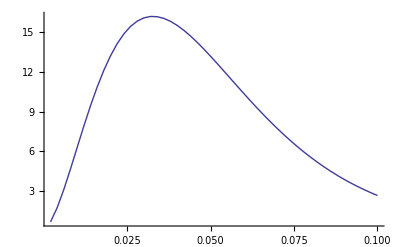

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5,listestrike,listprice,nb=50},
listestrike=Table[i/nb* 0.1,{i,1,nb}];
listprice=Table[CEVDensity [F, listestrike[[i]], vol, T, beta],{i,1,nb}];
    ListPlot[Transpose[{listestrike,listprice}],Joined->True]
]
```

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.3, T = 10},
  N[CEVCallDK0[F, vol, T, beta]]]]
```

{0.,0.15702}

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.3, T = 10,K=0.0001},
{CEVDensity [F, K, vol, T, beta],CEVDensity [F, 1.01K, vol, T, beta]}]]
```

{7.43766,{0.022674,0.0228193}}

```mathematica
Timing[Module[{F = 0.05, vol = 0.15, beta = 0.3, T = 10,K=0.0001},
{CEVDensity1[F, K, vol,0, T, beta],CEVDensity1 [F, 1.01K, vol,0, T, beta]}]]
```

{0.000312,{0.0240573,0.0241532}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than 30. digits of working precision to meet these tolerances.

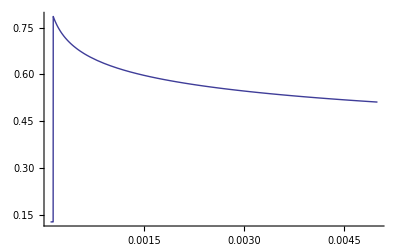

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5},
    Plot[{CEVBSVol[F, K, vol,0, T, beta]},{K,0.0001,0.005},PlotRange->All]]
```

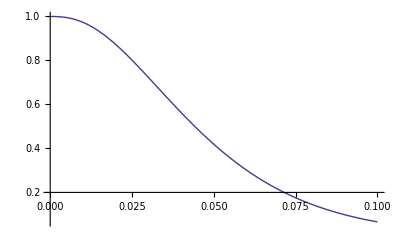

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5},
    Plot[{CEVDistribution[F, K, vol,0, T, beta]},{K,0.0001,0.1},PlotRange->All]]
```

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5},
    Plot[{CEVDistribution[F, K, vol,0, T, beta]},{K,0.0001,0.1},PlotRange->All]]
```

```mathematica
CEVDistribution[F_,K_,vol_,drift_,T_,beta_]:=Module[{shift=0.0001},(-CEVCall[F,K+shift,vol,drift,T,beta]+CEVCall[F,K-shift,vol,drift,T,beta])/(2shift)]
```

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.5, T = 25,K=0.06},
   {CEVDensity1[F, K, vol,0, T, beta]}]
```

{1478.89}

```mathematica
CEVDensity1[F_,K_,vol_,r_,T_,beta_]:=Module[{Sp,Kp,k=If[r==0,1/(2 vol^2(1-beta)^2 T),r/(vol^2(1-beta)(ⅇ^(r T(2-2beta))-1))]},
Sp=F^(2-2beta)ⅇ^(-r T(2-2beta))k;
Kp=K^(2-2beta)k;
(2-2beta)k^(1/(2-2beta))(Sp Kp^(1-4beta))^(1/(4-4beta))ⅇ^(-Sp-Kp)BesselI[1/(2-2beta),(2 √(Sp Kp))]
]
```

```mathematica
Module[{F = 0.35, vol = 0.05, beta = 0.0, T = 2.5,K=0.045},
    {CEVDensity1[F, K, vol,0, T, beta],CEVDensity[F,K,vol,T,beta]}]
```

```mathematica
Simplify[BesselI[1/2,x]]
```

(√(2/π) Sinh[x])/(√x)

### Integration Generique

```mathematica
LocalVolCall[CC_,CCDev1_,CCDev2_,CCInvInteg_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav},
fav=(F+K)/2;
w=1/(√(2 T))(CCInvInteg[K]-CCInvInteg[F]);
H1=2(ⅇ^(-w^2)+√(π w^2)(NormDis[√2 Abs[w]-1]));
H2=2/3(ⅇ^(-w^2)(1-2 w^2)-2(Abs[w])^3 √π(NormDis[√2 Abs[w]]-1));
Q=CC[fav]^2/4((CCDev2[fav]/CC[fav])-1/2(CCDev1[fav]/CC[fav])^2);
Max[F-K,0]+(√(CC[K] CC[F] T))/(2 √(2π))(H1+T H2 Q)
]
```

```mathematica
call=Max[f-K,0]+α/(2 √(2π))E^(1/4 α b1 ν ρ z^2)(f K)^(β/2)  (1-2 ν ρ z+ν^2 z^2)^(1/4) Re[(1/(2 √-κ)(ⅇ^(- √(-2κ) x) √π (1-ⅇ^(2  √(-2κ) x)+ⅇ^(2  √(-2κ) x) Erf[x/(√2 √T)+√-κ √T]-Erf[(√2 x-2 √-κ T)/(2 √T)])))];
```

```mathematica
LocalVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav,b1,b2,b3},
fav=(F+K)/2;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
Log[K/F]/(CCInvInteg[K]-CCInvInteg[F])(1+T (b3))
]
```

```mathematica
SABRCC[F_,alpha_,beta_]:=alpha F^beta
```

```mathematica
SABRCCDev1[F_,alpha_,beta_]:=alpha beta F^(beta-1)
```

```mathematica
SABRCCDev2[F_,alpha_,beta_]:=alpha  beta (beta-1)F^(beta-2)
```

```mathematica
SABRCCInvInteg[F_,alpha_,beta_]:=F^(1-beta)/((1-beta)alpha)
```

```mathematica
SABRCall[F_,K_,vol_,T_,beta_]:=
Module[{},
LocalVolCall[(SABRCC[#,vol,beta])&,(SABRCCDev1[#,vol,beta])&,(SABRCCDev2[#,vol,beta])&,(SABRCCInvInteg[#,vol,beta])&,F,K,T]
]
```

```mathematica
CEVVolApprox3[F_,K_,vol_,T_,beta_]:=
Module[{},
LocalVolBSVol[(SABRCC[#,vol,beta])&,(SABRCCDev1[#,vol,beta])&,(SABRCCDev2[#,vol,beta])&,(SABRCCInvInteg[#,vol,beta])&,0,0,F,K,T]
]
```

```mathematica
CEVVolApprox[F_,K_,vol_,T_,beta_]:=ImpVolBS[F,K,T,SABRCall[F,K,vol,T,beta]]
```

```mathematica
CEVVolApprox2[F_,K_,vol_,T_,beta_]:=Module[{fav=(F+K)/2},(vol (1-beta)Log[K/F])/(K^(1-beta)-F^(1-beta))(1+(beta-1)^2/24 vol^2 T fav^(2beta-2))]
```

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5, drift = 0.00001, K = 0.06},
    {CEVVolApprox[F, K, vol, T, beta],CEVVolApprox2[F, K, vol, T, beta],CEVVolApprox3[F, K, vol, T, beta], CEVBSVol[F,K,vol,0,T,beta]}]
```

{0.418176,0.358914,0.358914,0.358884}

General::unfl: Underflow occurred in computation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than 30. digits of working precision to meet these tolerances.

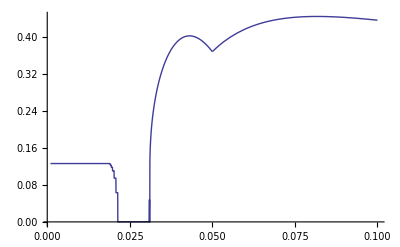

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.7, T = 2.5},
    Plot[{CEVVolApprox[F, K, vol, T, beta]},{K,0.001,0.1}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than 30. digits of working precision to meet these tolerances.

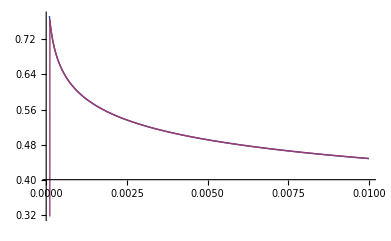

```mathematica
Module[{F = 0.05, vol = 0.15, beta = 0.71, T = 2.5},
    Plot[{CEVVolApprox2[F, K, vol, T, beta],CEVBSVol[F,K,vol,0,T,beta]},{K,0.0001,0.01}]]
```

```mathematica
ImpVolCEV[F_,K_,T_,beta_,discount_,opt_]:=Module[{r=Log[discount]/T,ss,vol=ImpVolBS[F,K,T,opt]},
ss=FindRoot[CEVVolApprox2[F, K, u, T, beta]==vol,{u,0.1,0.003,7.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss[[1,2]]]
```

```mathematica
Module[{F = 0.05, vol = 0.07, beta = .8, T = 20, drift = 0, K = 0.002,opt,volbeta,reopt},
opt=CEVCall[F,K,vol,drift,T,beta];
volbeta=ImpVolCEV[F,K,T,beta,1,opt]]
```

0.07001012824874838497120213066

```mathematica
SABRHaganVol[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat},z=(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Effetmat=(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T)/(1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
If[z==0,K^(-1+β) α Effetmat,
α/(f K)^((1-β)/2) z/x  Effetmat  ]]
```

## SABR LABORDERE

```mathematica
Integrate[Cos[x]/(a+Cos[x]+b Sin[x])^2,x]
```

-(2 ArcTan[(b+(-1+a) Tan[x/2])/(√(-1+a^2-b^2))])/((-1+a^2-b^2)^(3/2))+(b+a Sin[x])/((-1+a^2-b^2) (a+Cos[x]+b Sin[x]))

```mathematica
F1[x_,a_,b_]:=-(2 ArcTan[(b+(-1+a) Tan[x/2])/(√(-1+a^2-b^2))])/((-1+a^2-b^2)^(3/2))+(b+a Sin[x])/((-1+a^2-b^2) (a+Cos[x]+b Sin[x]))
```

```mathematica
F0[x_,a_,b_]:=Cos[x]/(a+Cos[x]+b Sin[x])
```

```mathematica
CC[f_]:=f^beta
```

```mathematica
q[f_]:=(f^(1-beta)-f0^(1-beta))/(1-beta)
```

```mathematica
amin[f_]:=√(alpha^2+2alpha nu rho q[f]+nu^2 q[f]^2)
```

```mathematica
CCamin[f_]:= CC[f] amin[f]
```

```mathematica
Simplify[D[CCamin[f],f]]
```

(f^(-1-beta) f0^(-2 beta) (alpha^2 (-1+beta)^2 beta f^(2 beta) f0^(2 beta)+(-f^beta f0+f f0^beta) (-beta f^beta f0+f f0^beta) nu^2+alpha (-1+beta) f^beta f0^beta (2 beta f^beta f0-f f0^beta-beta f f0^beta) nu rho))/((-1+beta)^2 √(alpha^2+((f^(1-beta)-f0^(1-beta))^2 nu^2)/(-1+beta)^2+(2 alpha (f^(1-beta)-f0^(1-beta)) nu rho)/(1-beta)))

```mathematica
Simplify[D[CCamin[f],f,f]]
```

(-1+beta) beta f^(-2+beta) √(alpha^2+((f^(1-beta)-f0^(1-beta))^2 nu^2)/(-1+beta)^2+(2 alpha (f^(1-beta)-f0^(1-beta)) nu rho)/(1-beta))-(f^(-3 beta) f0^(-2 beta) nu^2 (f f0^beta nu-f^beta (f0 nu+alpha (-1+beta) f0^beta rho))^2)/((-1+beta)^2 (alpha^2+((f^(1-beta)-f0^(1-beta))^2 nu^2)/(-1+beta)^2+(2 alpha (f^(1-beta)-f0^(1-beta)) nu rho)/(1-beta))^(3/2))+(2 beta f^(-1-beta) f0^-beta nu (-f f0^beta nu+f^beta (f0 nu+alpha (-1+beta) f0^beta rho)))/((-1+beta) √(alpha^2+((f^(1-beta)-f0^(1-beta))^2 nu^2)/(-1+beta)^2+(2 alpha (f^(1-beta)-f0^(1-beta)) nu rho)/(1-beta)))-(f^(-1-beta) f0^-beta nu (f f0^beta nu+alpha beta^2 f^beta f0^beta rho+beta (-2 f f0^beta nu+f^beta (f0 nu-alpha f0^beta rho))))/((-1+beta) √(alpha^2+((f^(1-beta)-f0^(1-beta))^2 nu^2)/(-1+beta)^2+(2 alpha (f^(1-beta)-f0^(1-beta)) nu rho)/(1-beta)))

```mathematica
Simplify[D[CCamin[f],f]/CCamin[f]]
```

(alpha^2 (-1+beta)^2 beta f^(2 beta) f0^(2 beta)+(-f^beta f0+f f0^beta) (-beta f^beta f0+f f0^beta) nu^2+alpha (-1+beta) f^beta f0^beta (2 beta f^beta f0-f f0^beta-beta f f0^beta) nu rho)/(f (alpha^2 (-1+beta)^2 f^(2 beta) f0^(2 beta)+(f^beta f0-f f0^beta)^2 nu^2+2 alpha (-1+beta) f^beta f0^beta (f^beta f0-f f0^beta) nu rho))

```mathematica
Simplify[D[CCamin[f],f,f]/CCamin[f]]
```

((-1+beta) f^(-2+beta) (alpha^4 (-1+beta)^4 beta f^(3 beta) f0^(4 beta)+beta f0 (f^beta f0-f f0^beta)^3 nu^4+alpha^3 (-1+beta)^3 beta f^(2 beta) f0^(3 beta) (4 f^beta f0-3 f f0^beta) nu rho-alpha (-1+beta) beta f0^beta (f^beta f0-f f0^beta)^2 (-4 f^beta f0+f f0^beta) nu^3 rho+alpha^2 (-1+beta)^2 f^beta f0^(2 beta) nu^2 (f^2 f0^(2 beta) (-1+rho^2)+beta (f^2 f0^(2 beta) (2+rho^2)+2 f^(2 beta) f0^2 (1+2 rho^2)-3 f^(1+beta) f0^(1+beta) (1+2 rho^2)))))/(alpha^2 (-1+beta)^2 f^(2 beta) f0^(2 beta)+(f^beta f0-f f0^beta)^2 nu^2+2 alpha (-1+beta) f^beta f0^beta (f^beta f0-f f0^beta) nu rho)^2

```mathematica
SABRLabordere[f0_,f_,T_,alpha_,beta_,rho_,nu_]:=
Module[{c1,c2,amin,cf,df,q,sigma1,volf,A,B,Ap,theta1,theta2,theta2prime,LnP},
c1=(alpha^2 (-1+beta)^2 beta f^(2 beta) f0^(2 beta)+(-f^beta f0+f f0^beta) (-beta f^beta f0+f f0^beta) nu^2+alpha (-1+beta) f^beta f0^beta (2 beta f^beta f0-f f0^beta-beta f f0^beta) nu rho)/(f (alpha^2 (-1+beta)^2 f^(2 beta) f0^(2 beta)+(f^beta f0-f f0^beta)^2 nu^2+2 alpha (-1+beta) f^beta f0^beta (f^beta f0-f f0^beta) nu rho));
c2=((-1+beta) f^(-2+beta) (alpha^4 (-1+beta)^4 beta f^(3 beta) f0^(4 beta)+beta f0 (f^beta f0-f f0^beta)^3 nu^4+alpha^3 (-1+beta)^3 beta f^(2 beta) f0^(3 beta) (4 f^beta f0-3 f f0^beta) nu rho-alpha (-1+beta) beta f0^beta (f^beta f0-f f0^beta)^2 (-4 f^beta f0+f f0^beta) nu^3 rho+alpha^2 (-1+beta)^2 f^beta f0^(2 beta) nu^2 (f^2 f0^(2 beta) (-1+rho^2)+beta (f^2 f0^(2 beta) (2+rho^2)+2 f^(2 beta) f0^2 (1+2 rho^2)-3 f^(1+beta) f0^(1+beta) (1+2 rho^2)))))/(alpha^2 (-1+beta)^2 f^(2 beta) f0^(2 beta)+(f^beta f0-f f0^beta)^2 nu^2+2 alpha (-1+beta) f^beta f0^beta (f^beta f0-f f0^beta) nu rho)^2;
cf=f^beta;
;
q=(f^(1-beta)-f0^(1-beta))/(1-beta);
amin=√(alpha^2+2alpha nu rho q+nu^2 q^2);
df=ArcCosh[(-q nu rho-alpha rho^2+amin)/(alpha(1-rho^2))];

theta1=ArcTan[-(√(1-rho^2))/rho];
theta2=ArcTan[-(alpha √(1-rho^2))/(alpha rho+nu q)];
theta2prime=(√(1-rho^2))/(nu q+rho(alpha-amin));
A=(f^(1-beta)nu)/((1-beta)amin);
B=rho/(√(1-rho^2));
Ap=(f nu(alpha rho+nu q)+f^beta(beta-1)amin^2)/((beta-1)f^beta amin^2(nu q+rho(alpha-amin)));
LnP=(beta rho)/(2 √(1-rho^2)(1-beta))(F0[theta2,A,B]theta2prime-F0[theta1,A,B]theta2prime-Ap(F1[theta2,A,B]-F1[theta1,A,B]));
sigma1=(cf amin)^2/24(1/f^2+2c2-c1^2)+(alpha nu^2 LnP(1-rho^2)Sinh[df])/(2df);
volf=1/nu Log[(q nu+alpha rho+√(alpha^2+q^2 nu^2+2q alpha nu rho))/(alpha(1+rho))];
Log[f/f0]/volf(1+sigma1((f+f0)/2)T)

]
```

```mathematica
Manipulate[Module[{f0=0.05},
Plot[{SABRLabordere[f0,K,T,alpha,beta,rho,nu],SABRHaganVol[f0,alpha,beta,rho,nu,K,T]},{K,0.001,0.12},PlotLegend->{"L","Hagan"},LegendPosition->{1.1,-0.4},PlotRange->{0.1,0.7}]],
{{T,5},0.5,30,0.5},
{{nu,1},0.01,3,0.01},
{{beta,0.7},0.1,0.99,0.01},
{{rho,-0.5},-0.99,0.99,0.01},
{{alpha,0.1},0.001,0.3}]
```

Plot::optx: Unknown option PlotLegends`PlotLegend in Plot[{SABRLabordere[f0$527, K, FE`T$$2, FE`alpha$$2, FE`beta$$2, FE`rho$$2, FE`nu$$2], SABRHaganVol[f0$527, « 5 », « 7 »]}, « 4 »].

Plot::optx: Unknown option PlotLegends`PlotLegend in Plot[{SABRLabordere[f0$630, K, FE`T$$19, FE`alpha$$19, FE`beta$$19, FE`rho$$19, FE`nu$$19], SABRHaganVol[« 1 »]}, « 3 », « 9 » → « 1 »].

Plot::optx: Unknown option PlotLegends`PlotLegend in Plot[{SABRLabordere[f0$133, K, FE`T$$2, FE`alpha$$2, FE`beta$$2, FE`rho$$2, FE`nu$$2], SABRHaganVol[f0$133, « 5 », « 7 »]}, « 4 »].

## SABR TRONQUE A LA PARIBAS

```mathematica
Simplify[1/((1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))F^β1+F^β2(1-1/(1+F^(β1-β2)(ⅇ^(λ F)-1))))]
```

ⅇ^(-F λ) F^(-β1-β2) ((-1+ⅇ^(F λ)) F^β1+F^β2)

```mathematica
Integrate[ⅇ^(-F λ) F^(-β1-β2) ((-1+ⅇ^(F λ)) F^β1+F^β2),F]
```

(-F^-β1 (F λ)^β1 Gamma[1-β1,F λ]+(F^-β2 (-F λ+(-1+β2) (F λ)^β2 Gamma[1-β2,F λ]))/(-1+β2))/λ

```mathematica
zzp[F_,K_,β1_,β2_,λ_]:=(F^(1-β2)-K^(1-β2))/(1-β2)+λ^(β1-1) (-Gamma[1-β1,F λ]+Gamma[1-β1,K λ])+λ^(β2-1) (Gamma[1-β2,F λ]-Gamma[1-β2,K λ])
```

```mathematica
FullSimplify[-F^-β1 (F λ)^β1 Gamma[1-β1,F λ]+(F^-β2 (-F λ+(-1+β2) (F λ)^β2 Gamma[1-β2,F λ]))/(-1+β2)-(-K^-β1 (K λ)^β1 Gamma[1-β1,K λ]+(K^-β2 (-K λ+(-1+β2) (K λ)^β2 Gamma[1-β2,K λ]))/(-1+β2)),λ>0]
```

((F^(1-β2)-K^(1-β2)) λ)/(1-β2)+λ^β1 (-Gamma[1-β1,F λ]+Gamma[1-β1,K λ])+λ^β2 (Gamma[1-β2,F λ]-Gamma[1-β2,K λ])

```mathematica
(-F^-β1 (F λ)^β1 Gamma[1-β1,F λ]+(F^-β2 (-F λ+(-1+β2) (F λ)^β2 Gamma[1-β2,F λ]))/(-1+β2))/λ/.F->K
```

(-K^-β1 (K λ)^β1 Gamma[1-β1,K λ]+(K^-β2 (-K λ+(-1+β2) (K λ)^β2 Gamma[1-β2,K λ]))/(-1+β2))/λ

```mathematica
Simplify[1/D[zzp[F,k,β1,β2,λ],F],λ>0]
```

(ⅇ^(F λ) F^(β1+β2))/((-1+ⅇ^(F λ)) F^β1+F^β2)

```mathematica
zz0[K_,F0_,β_]:=F0^(1-β)/(-1+β)-K^(1-β)/(-1+β)
```

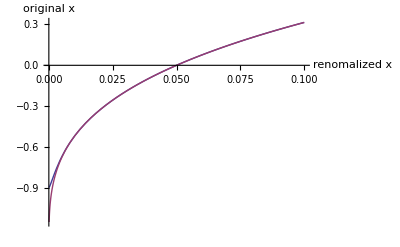

```mathematica
Module[{F0=0.05,β1=0.1,β2=0.7,λ=500},
Plot[{zzp[K,F0,β1,β2,λ],zz0[K,F0,β2]},{K,0.0001,0.1},PlotLegend->{"F_(β1, β2)","F_0"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

```mathematica
StochVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav,b1,b2,b3,x,z},
fav=√(F K);
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 CCDev1[fav] ν ρ;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
z=(CCInvInteg[F]-CCInvInteg[K]);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Log[F/K]/x(1+T (b1+b2+b3))
]
```

```mathematica
StochVolBSVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 CCDev1[fav] ν ρ;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
z=(CCInvInteg[F]-CCInvInteg[K]);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]]/F(1+T (b1+b2+b3)),Abs[Log[F/K]/x] (1+T (b1+b2+b3))]
]
```

```mathematica
StochVolNormVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_]:=Module[{w,H1,H2,Q,fav,b1,b2,b3,x,z},
fav=(F+K)/2;
b1=1/24 ν^2 (2-3 ρ^2);
b2=1/4 CCDev1[fav] ν ρ;
b3=(CC[fav])^2/24((2CCDev2[fav])/CC[fav]-(CCDev1[fav]/CC[fav])^2+1/fav^2);
z=(CCInvInteg[F]-CCInvInteg[K]);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Abs[(K-F)/x](1+T (b1+b2+b3))
]
```

```mathematica
quand F->K , (∫_K)^F dx/C[x]≈ (F-K)/C[F]
```

```mathematica
StochVolNormVol[CC_,CCDev1_,CCDev2_,CCInvInteg_,ρ_,ν_,F_,K_,T_,fav_]:=Module[{w,H1,H2,Q,b1,b2,b3,x,z},
b1=1/24 ν^2 (2-3 ρ^2);b2=1/4 CCDev1[fav] ν ρ;b3=1/24  (2 CCDev2[fav]CC[fav]-(CCDev1[fav])^2+1);
z=CCInvInteg[F]-CCInvInteg[K];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
If[Abs[F-K]<10^-7,Abs[CC[F]] (1+T (b1+b2+b3)),Abs[(K-F)/x] (1+T (b1+b2+b3))]]
```

```mathematica
SABRCC[F_,alpha_,beta_]:=alpha F^beta
```

```mathematica
SABRCCDev1[F_,alpha_,beta_]:=alpha beta F^(beta-1)
```

```mathematica
SABRCCDev2[F_,alpha_,beta_]:=alpha  beta (beta-1)F^(beta-2)
```

```mathematica
SABRCCInvInteg[F_,alpha_,beta_]:=F^(1-beta)/((1-beta)alpha)
```

```mathematica
SABRCallBSVolApprox[F_,K_,vol_,T_,beta_,ρ_,ν_]:=
Module[{},
StochVolBSVol[(SABRCC[#,vol,beta])&,(SABRCCDev1[#,vol,beta])&,(SABRCCDev2[#,vol,beta])&,(SABRCCInvInteg[#,vol,beta])&,ρ,ν,F,K,T,√(F K)]
]
```

```mathematica
SABRCallNormVol[F_,K_,alpha_,T_,beta_,ρ_,ν_]:=
Module[{},
StochVolNormVol[(SABRCC[#,alpha,beta])&,(SABRCCDev1[#,alpha,beta])&,(SABRCCDev2[#,alpha,beta])&,(SABRCCInvInteg[#,alpha,beta])&,ρ,ν,F,K,T,(F+K)/2]
]
```

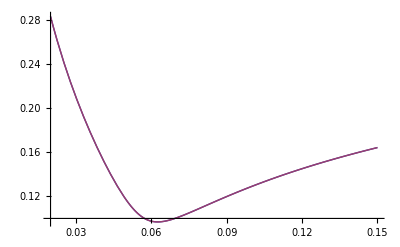

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[{SABRCallBSVolApprox[f,K,α,T,β,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15}]]
```

```mathematica
Module[{f=0.05,α=0.0248,T=1,β=0.5,ATMvol,ρ=-0.56,ν=0.5,K=0.05},
{SABRCallBSVolApprox[f,K,α,T,β,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]}]
```

{0.111716,0.111716}

```mathematica
Simplify[D[α ((1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))F^β1+F^β2(1-1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))),F]]
```

(ⅇ^(F λ) F^(-1+β1+β2) α (F^β2 β1+(-1+ⅇ^(F λ)) F^β1 β2-F^(1+β1) λ+F^(1+β2) λ))/(((-1+ⅇ^(F λ)) F^β1+F^β2)^2)

```mathematica
Simplify[D[α ((1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))F^β1+F^β2(1-1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))),F,F]]
```

1/(((-1+ⅇ^(F λ)) F^β1+F^β2)^3)ⅇ^(F λ) F^(-2+β1+β2) α (F^(2 β2) (-1+β1) β1+(-1+ⅇ^(F λ))^2 F^(2 β1) (-1+β2) β2-(-1+ⅇ^(F λ)) F^(β1+β2) (β1+β1^2+β2-4 β1 β2+β2^2)+2 F^(1+2 β2) β1 λ-2 (-1+ⅇ^(F λ)) F^(1+2 β1) β2 λ-2 F^(1+β1+β2) (β1+ⅇ^(F λ) β1+β2-2 ⅇ^(F λ) β2) λ+(1+ⅇ^(F λ)) F^(2+2 β1) λ^2-(2+ⅇ^(F λ)) F^(2+β1+β2) λ^2+F^(2+2 β2) λ^2)

```mathematica
PSABRCC[F_,K_,α_,β1_,β2_,λ_]:=α ((1/(1+F^(β1-β2)(ⅇ^(λ F)-1)))F^β1+F^β2(1-1/(1+F^(β1-β2)(ⅇ^(λ F)-1))))
```

```mathematica
PSABRCCDev1[F_,K_,α_,β1_,β2_,λ_]:=(ⅇ^(F λ) F^(-1+β1+β2) α (F^β2 β1+(-1+ⅇ^(F λ)) F^β1 β2-F^(1+β1) λ+F^(1+β2) λ))/(((-1+ⅇ^(F λ)) F^β1+F^β2)^2)
```

```mathematica
PSABRCCDev2[F_,K_,α_,β1_,β2_,λ_]:=1/(((-1+ⅇ^(F λ)) F^β1+F^β2)^3)ⅇ^(F λ) F^(-2+β1+β2) α (F^(2 β2) (-1+β1) β1+(-1+ⅇ^(F λ))^2 F^(2 β1) (-1+β2) β2-(-1+ⅇ^(F λ)) F^(β1+β2) (β1+β1^2+β2-4 β1 β2+β2^2)+2 F^(1+2 β2) β1 λ-2 (-1+ⅇ^(F λ)) F^(1+2 β1) β2 λ-2 F^(1+β1+β2) (β1+ⅇ^(F λ) β1+β2-2 ⅇ^(F λ) β2) λ+(1+ⅇ^(F λ)) F^(2+2 β1) λ^2-(2+ⅇ^(F λ)) F^(2+β1+β2) λ^2+F^(2+2 β2) λ^2)
```

```mathematica
PSABRCCInvInteg[F_,K_,α_,β1_,β2_,λ_]:=1/α((F^(1-β2)-K^(1-β2))/(1-β2)+λ^(β1-1) (-Gamma[1-β1,F λ]+Gamma[1-β1,K λ])+λ^(β2-1) (Gamma[1-β2,F λ]-Gamma[1-β2,K λ]))
```

```mathematica
PSABRCallBSVol[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=
Module[{fav=F},
StochVolBSVol[(PSABRCC[F,#,α,β1,β2,λ])&,(PSABRCCDev1[F,#,α,β1,β2,λ])&,(PSABRCCDev2[F,#,α,β1,β2,λ])&,(PSABRCCInvInteg[F,#,α,β1,β2,λ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
PSABRCallBSOption[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=BS[K,K,T,PSABRCallBSVol[F,K,α,T,β1,β2,λ,ρ,ν]]
```

```mathematica
PSABRCallBSDigitale[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=Module[{s1,s2,shift=0.00001},
s1=PSABRCallBSOption[F,K+shift,α,T,β1,β2,λ,ρ,ν];
s2=PSABRCallBSOption[F,K-shift,α,T,β1,β2,λ,ρ,ν];
(s2-s1)/(2shift)
]
```

```mathematica
PSABRCallNormVol[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=
Module[{fav=F},
StochVolNormVol[(PSABRCC[#,F,α,β1,β2,λ])&,(PSABRCCDev1[#,F,α,β1,β2,λ])&,(PSABRCCDev2[#,F,α,β1,β2,λ])&,(PSABRCCInvInteg[#,F,α,β1,β2,λ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
PSABRCallNormOption[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=NormalCall[F,PSABRCallNormVol[F,K,α,T,β1,β2,λ,ρ,ν],K,T]
```

```mathematica
PSABRCallNormDigitale[F_,K_,α_,T_,β1_,β2_,λ_,ρ_,ν_]:=Module[{s1,s2,shift=0.00001},
s1=PSABRCallNormOption[F,K+shift,α,T,β1,β2,λ,ρ,ν];
s2=PSABRCallNormOption[F,K-shift,α,T,β1,β2,λ,ρ,ν];
(s2-s1)/(2shift)]
```

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,β1=0.5,β2=0.6,λ=100,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0000001,K=0.04},
PSABRCallBSVol[f,K,α,T,β1,β2,λ,ρ,ν]]
```

0.0812006

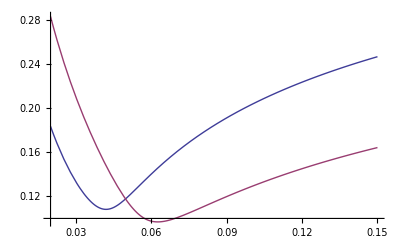

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,β1=0.01,β2=0.5,λ=100,ATMvol,ρ=-0.56,ν=0.45},
Plot[{PSABRCallBSVol[f,K,α,T,β1,β2,λ,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15},
PlotLegend->{"PSABR","Hagan"},LegendPosition->{1.,-0.5}]]
```

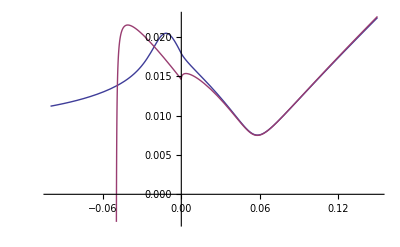

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,β1=0.01,β2=0.5,λ=100,ρ=-0.56,ν=0.5},
Plot[{PSABRCallNormVol[f,K,α,T,β1,β2,λ,ρ,ν],SABRCallNormVol[f,K,α,T,β,ρ,ν]},{K,-0.1,0.15},
PlotLegend->{"PSABR","Hagan"},LegendPosition->{1.,-0.5}]]
```

## Epsilon SABR

```mathematica
ESABRCC[F_,alpha_,beta_,ϵ_]:=alpha (ϵ+F)^beta
```

```mathematica
ESABRCCDev1[F_,alpha_,beta_,ϵ_]:=alpha beta (ϵ+F)^(beta-1)
```

```mathematica
ESABRCCDev2[F_,alpha_,beta_,ϵ_]:=alpha  beta (beta-1)(ϵ+F)^(beta-2)
```

```mathematica
ESABRCCInvInteg[F_,alpha_,β_,ϵ_]:=(F ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ])/alpha
```

```mathematica
ESABRCallBSVol[F_,K_,vol_,T_,beta_,ρ_,ν_,ϵ_]:=
Module[{},
StochVolBSVol[(ESABRCC[#,vol,beta,ϵ])&,(ESABRCCDev1[#,vol,beta,ϵ])&,(ESABRCCDev2[#,vol,beta,ϵ])&,(ESABRCCInvInteg[#,vol,beta,ϵ])&,ρ,ν,F,K,T]
]
```

```mathematica
ESABRCallNormVol[F_,K_,alpha_,T_,beta_,ρ_,ν_,ϵ_]:=
Module[{},
StochVolNormVol[(ESABRCC[#,alpha,beta,ϵ])&,(ESABRCCDev1[#,alpha,beta,ϵ])&,(ESABRCCDev2[#,alpha,beta,ϵ])&,(ESABRCCInvInteg[#,alpha,beta,ϵ])&,ρ,ν,F,K,T,F]
]
```

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.5,K=0.128,ϵ=0.001},
{ESABRCallBSVol[f,K,α,T,β,ρ,ν,ϵ],SABRCallBSVolApprox[f,K,α,T,β,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]}]
```

{0.16607,0.163795,0.162297}

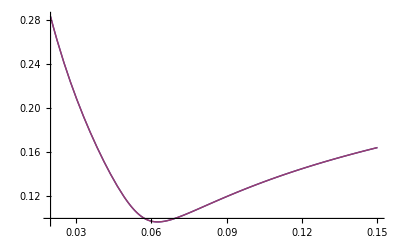

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0000001},
Plot[{ESABRCallBSVol[f,K,α,T,β,ρ,ν,ϵ],SABRHaganVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.15},
PlotLegend->{"F_ϵ","Hagan"},LegendPosition->{1.,-0.5}]]
```

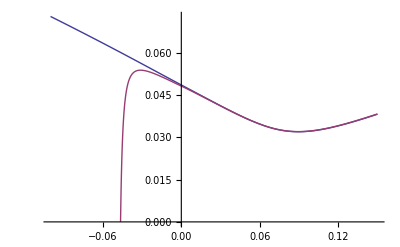

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.01,ATMvol,ρ=-0.56,ν=0.5,ϵ=0.0001},
Plot[{ESABRCallNormVol[f,K,α,T,β,ρ,ν,ϵ],SABRCallNormVol[f,K,α,T,β,ρ,ν]},{K,-0.1,0.15},
PlotLegend->{"F_ϵ","Hagan"},LegendPosition->{1.,-0.5}]]
```

```mathematica
Module[{f=0.05,α=0.00248,T=20,β=0.1,ATMvol,ρ=-0.56,ν=0.15,ϵ=0.00001,K=0.02},
{ESABRCallNormVol[f,K,α,T,β,ρ,ν,ϵ],SABRCallNormVol[f,K,α,T,β,ρ,ν]}]
```

{0.00595355,0.00595185}

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.5,K=0.-0.05,ϵ=0.00001},
{ESABRCallBSVol[f,K,α,T,β,ρ,ν,ϵ],SABRCallBSVolApprox[f,K,α,T,β,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]}]
```

{-0.0136346+0.5643 ⅈ,-0.163635+0.558394 ⅈ,-0.181744+0.620188 ⅈ}

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.1,ATMvol,ρ=-0.56,ν=0.5,K=-0.02,ϵ=0.0001},
{ESABRCallNormVol[f,K,α,T,β,ρ,ν,ϵ],SABRCallNormVol[f,K,α,T,β,ρ,ν],SABRHaganVol[f,α,β,ρ,ν,K,T]}]
```

{0.0419942,0.0374262,-0.122364-1.29111 ⅈ}

## SABR epsilon avec controle a l'infini

```mathematica
f[F_]:=F ϵ^(-β/2) Hypergeometric2F1[1/2,β/2,3/2,-F^2/ϵ]
```

```mathematica
CC[F_,β_,ϵ_]:=(F^2+ϵ)^(β/2)
```

```mathematica
1/Simplify[D[f[F],F],ϵ>0]
```

(F^2+ϵ)^(β/2)

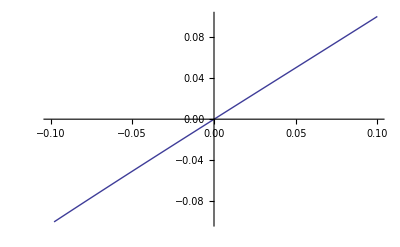
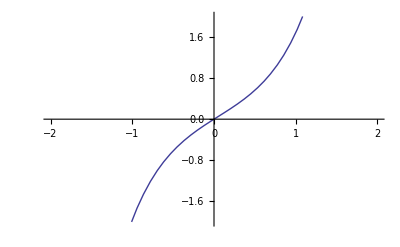

```mathematica
Module[{γ=0.5,F0=0.05},{Plot[γ Sinh[(F-F0)/γ]+F0,{F,-0.1,0.1},PlotRange->{-0.1,0.1}],Plot[γ Sinh[(F-F0)/γ]+F0,{F,-2,2},PlotRange->{-2,2}]}]
```

```mathematica
f1[F_,γ_,F0_]:=f[γ Sinh[(F-F0)/γ]+F0]-f[F0]
```

```mathematica
Simplify[f[γ Sinh[(F-F0)/γ]+F0]-f[F0]]
```

ϵ^(-β/2) (-F0 Hypergeometric2F1[1/2,β/2,3/2,-F0^2/ϵ]+Hypergeometric2F1[1/2,β/2,3/2,-(F0+γ Sinh[(F-F0)/γ])^2/ϵ] (F0+γ Sinh[(F-F0)/γ]))

```mathematica
1/Simplify[D[f1[F,γ,F0],F],ϵ>0]
```

Sech[(F-F0)/γ] (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2)

```mathematica
zz0[F0,F0,β]
```

0

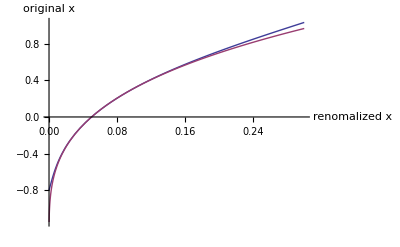

```mathematica
Module[{F0=0.05,β=0.7,ϵ=0.00004,γ=0.3},
Plot[{ϵ^(-β/2) (-F0 Hypergeometric2F1[1/2,β/2,3/2,-F0^2/ϵ]+Hypergeometric2F1[1/2,β/2,3/2,-(F0+γ Sinh[(K-F0)/γ])^2/ϵ] (F0+γ Sinh[(K-F0)/γ])),zz0[K,F0,β]},{K,0.0001,0.3},PlotLegend->{"F_(ϵ, γ)","F_0"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

```mathematica
CC[F_,β_,ϵ_,γ_,F0_]:= Sech[(F-F0)/γ] (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2)
```

```mathematica
Simplify[D[CC[F,β,ϵ,γ,F0],F]]
```

(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) ((β (F0+γ Sinh[(F-F0)/γ]))/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(Sech[(F-F0)/γ] Tanh[(F-F0)/γ])/γ)

```mathematica
Simplify[D[CC[F,β,ϵ,γ,F0],F,F]]
```

(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) (-Sech[(F-F0)/γ]^3/γ^2+((-2+β) β Cosh[(F-F0)/γ] (F0+γ Sinh[(F-F0)/γ])^2)/(ϵ^2 (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ)^2)+(β Cosh[(F-F0)/γ])/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(β (F0+γ Sinh[(F-F0)/γ]) Tanh[(F-F0)/γ])/(γ ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))+(Sech[(F-F0)/γ] Tanh[(F-F0)/γ]^2)/γ^2)

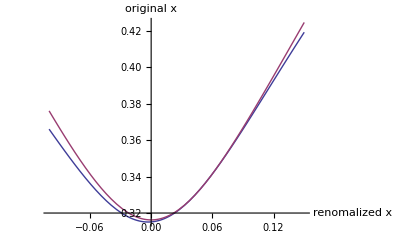

```mathematica
Module[{γ=0.6,ϵ=0.01,β=0.5,F0=0.05},Plot[{CC[F,β,ϵ,γ,F0],CC[F,β,ϵ]},{F,-0.1,0.15},PlotLegend->{"F_(ϵ, γ)","F_ϵ"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

```mathematica
EZSABRCC[F_,F0_,α_,β_,ϵ_,γ_]:=α Sech[(F-F0)/γ] (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2)
```

```mathematica
EZSABRCCDev1[F_,F0_,α_,β_,ϵ_,γ_]:=α (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) ((β (F0+γ Sinh[(F-F0)/γ]))/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(Sech[(F-F0)/γ] Tanh[(F-F0)/γ])/γ)
```

```mathematica
EZSABRCCDev2[F_,F0_,α_,β_,ϵ_,γ_]:=α (ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))^(β/2) (-Sech[(F-F0)/γ]^3/γ^2+((-2+β) β Cosh[(F-F0)/γ] (F0+γ Sinh[(F-F0)/γ])^2)/(ϵ^2 (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ)^2)+(β Cosh[(F-F0)/γ])/(ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))-(β (F0+γ Sinh[(F-F0)/γ]) Tanh[(F-F0)/γ])/(γ ϵ (1+(F0+γ Sinh[(F-F0)/γ])^2/ϵ))+(Sech[(F-F0)/γ] Tanh[(F-F0)/γ]^2)/γ^2)
```

```mathematica
EZSABRCCInvInteg[F_,F0_,α_,β_,ϵ_,γ_]:=1/α  ϵ^(-β/2) (Hypergeometric2F1[1/2,β/2,3/2,-(F0+γ Sinh[(F-F0)/γ])^2/ϵ] (F0+γ Sinh[(F-F0)/γ]))
```

```mathematica
EZSABRCallBSVol[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=
Module[{fav=F},
StochVolBSVol[(EZSABRCC[#,F,α,β,ϵ,γ])&,(EZSABRCCDev1[#,F,α,β,ϵ,γ])&,(EZSABRCCDev2[#,F,α,β,ϵ,γ])&,(EZSABRCCInvInteg[#,F,α,β,ϵ,γ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
EZSABRCallBSOption[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=BS[K,K,T,EZSABRCallBSVol[F,K,α,T,β,ρ,ν,ϵ,γ]]
```

```mathematica
EZSABRCallBSDigitale[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=Module[{s1,s2,shift=0.00001},
s1=EZSABRCallBSOption[F,K+shift,α,T,β,ρ,ν,ϵ,γ];
s2=EZSABRCallBSOption[F,K-shift,α,T,β,ρ,ν,ϵ,γ];
(s2-s1)/(2shift)
]
```

```mathematica
EZSABRCallNormVol[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=
Module[{fav=F},
StochVolNormVol[(EZSABRCC[#,F,α,β,ϵ,γ])&,(EZSABRCCDev1[#,F,α,β,ϵ,γ])&,(EZSABRCCDev2[#,F,α,β,ϵ,γ])&,(EZSABRCCInvInteg[#,F,α,β,ϵ,γ])&,ρ,ν,F,K,T,fav]
]
```

```mathematica
SABRHaganDigitale[F_,K_,α_,T_,β_,ρ_,ν_]:=Module[{s1,s2,shift=0.00001},
s1=SABRHaganOption[F,α,β,ρ,ν,K+shift,T];
s2=SABRHaganOption[F,α,β,ρ,ν,K-shift,T];
(s2-s1)/(2shift)]
```

```mathematica
EZSABRCallNormOption[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=NormalCall[F,EZSABRCallNormVol[F,K,α,T,β,ρ,ν,ϵ,γ],K,T]
```

```mathematica
EZSABRCallNormDigitale[F_,K_,α_,T_,β_,ρ_,ν_,ϵ_,γ_]:=Module[{s1,s2,shift=0.00001},
s1=EZSABRCallNormOption[F,K+shift,α,T,β,ρ,ν,ϵ,γ];
s2=EZSABRCallNormOption[F,K-shift,α,T,β,ρ,ν,ϵ,γ];
(s2-s1)/(2shift)]
```

ss={α1$2453→0.0245416}

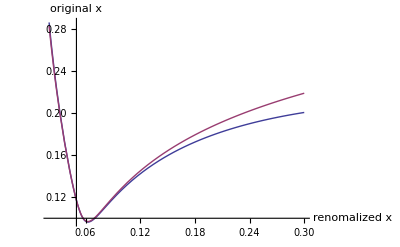

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.15,α1,ss},
ss=FindRoot[EZSABRCallBSVol[f,f,α1,T,β,ρ,ν,ϵ,γ]==SABRHaganVol[f,α,β,ρ,ν,f,T],{α1,α}];
Print["ss=",ss];α1=α1/.ss;
Plot[{EZSABRCallBSVol[f,K,α1,T,β,ρ,ν,ϵ,γ],SABRHaganVol[f,α,β,ρ,ν,K,T]},{K,0.02,0.3},PlotLegend->{"F_(ϵ, γ)","F_Hagan"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]]
```

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.15,α1,ss,K=0.045},
ss=FindRoot[EZSABRCallBSVol[f,f,α1,T,β,ρ,ν,ϵ,γ]==SABRHaganVol[f,α,β,ρ,ν,f,T],{α1,α}];
Print["ss=",ss];α1=α1/.ss;
{EZSABRCallNormVol[f,f,α1,T,β,ρ,ν,ϵ,γ],SABRCallNormVol[f,K,α,T,β,ρ,ν]}]
```

ss={α1$168276→0.0245416}

{0.00813511,0.00893175}

```mathematica
Module[{f=0.05,α=0.0248,T=10,β=0.5,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.15,α1,ss,K=0.045},
{EZSABRCallNormDigitale[f,f,α,T,β,ρ,ν,ϵ,γ],EZSABRCallBSDigitale[f,f,α,T,β,ρ,ν,ϵ,γ]}]
```

{0.785455,0.128435}

```mathematica
Manipulate[Module[{ρ=-0.56,ν=0.45,ϵ=0.001,α0,α1,α2,ss1,ss2},
α0=f^(1-β) σATM;
ss1=FindRoot[SABRHaganVol[f,α1,β,ρ,ν,f,T]==σATM,{α1,α0}];
α1=α1/.ss1;
ss2=FindRoot[EZSABRCallNormVol[f,f,α2,T,β,ρ,ν,ϵ,γ]==SABRCallNormVol[f,f,α1,T,β,ρ,ν],{α2,α0}];
α2=α2/.ss2;
Plot[{EZSABRCallNormVol[f,K,α1,T,β,ρ,ν,ϵ,γ],SABRCallNormVol[f,K,α2,T,β,ρ,ν]},{K,-0.05,0.1},
PlotLegend->{"F_(ϵ, γ)","F_Hagan"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]],
{{f,0.02},0.001,0.1,0.001},
{{σATM,0.15},0.01,0.5,0.01},
{{β,0.5},0.001,0.8,0.005},{{T,5},0.5,30,0.5},{{γ,0.8},0.1,3,0.05}]
```

```mathematica
Module[{f=0.02,α0,σATM=0.15,T=5,β=0.01,ATMvol,ρ=-0.56,ν=0.45,ϵ=0.0001,γ=0.8
,α1,α2,ss1,ss2,fcalib=0.02,K=0.04},
α0=f^(1-β) σATM;Print["α0=",α0];
ss1=FindRoot[EZSABRCallBSVol[f,fcalib,α1,T,β,ρ,ν,ϵ,γ]==σATM,{α1,α0}];
α1=α1/.ss1;Print["α1=",α1];
ss2=FindRoot[SABRHaganVol[f,α2,β,ρ,ν,f,T]==σATM,{α2,α0}];
α2=α2/.ss2;Print["α2=",α2];
SABRHaganDigitale[f,K,α2,T,β,ρ,ν]]
```

α0=0.00311969

α1=0.00297194

α2=0.00297562

0.00351385

```mathematica
Manipulate[Module[{α0,ρ=-0.56,ν=0.45,ϵ=0.0001
,α1,α2,ss1,ss2,fcalib=0.02},
α0=f^(1-β) σATM;
ss1=FindRoot[EZSABRCallBSVol[f,fcalib,α1,T,β,ρ,ν,ϵ,γ]==σATM,{α1,α0}];
α1=α1/.ss1;
ss2=FindRoot[SABRHaganVol[f,α2,β,ρ,ν,f,T]==σATM,{α2,α0}];
α2=α2/.ss2;
Plot[{EZSABRCallNormDigitale[f,K,α1,T,β,ρ,ν,ϵ,γ],SABRHaganDigitale[f,K,α2,T,β,ρ,ν],1},{K,-0.03,0.08},PlotRange->{0,1},
PlotLegend->{"F_(ϵ, γ)","F_Hagan"},LegendPosition->{1.,-0.5},AxesLabel->{"renomalized x","original x"}]],
{{f,0.02},0.001,0.1,0.001},
{{σATM,0.15},0.01,0.5,0.01},
{{β,0.5},0.001,0.8,0.005},{{T,5},0.5,30,0.5},{{γ,0.8},0.1,3,0.05}]
```